```mathematica
SetDirectory[NotebookDirectory[]]
Needs["SSS`"]
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

### Manual constructing a ruleset to create a specified n-dimensional network

#### Constructing a constant-width band (1-d case): one rule that creates a diagonal path across a SSS, creating and destroying a series of cells, and would die out without another rule to start over. Here the number of As defines the width of the band, but the band remains one-dimensional.



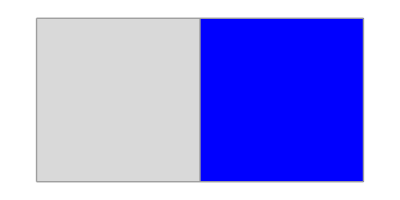
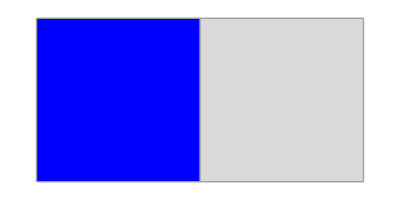
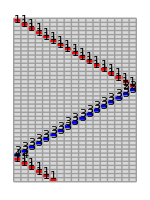
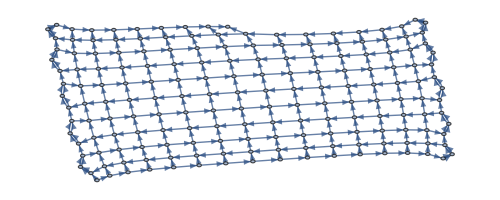
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","AB"->"AF","AF"->"FA","FA"->"BA"},"BAAAAAAAAAAAAAAAA",200,SSSMax->40,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,NetMax->179,VertexLabels->Placed["Name",Tooltip]];
```

#### This related ruleset changes width depending on the number of Bs, and edge behavior depending on the number of As, but is still one-dimensional:

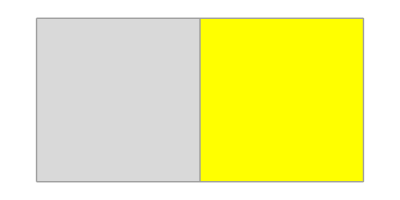
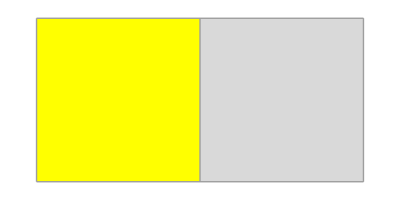
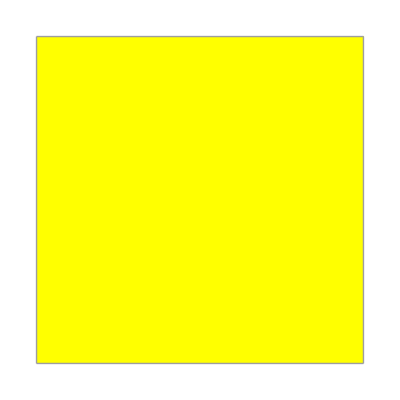

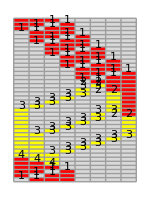
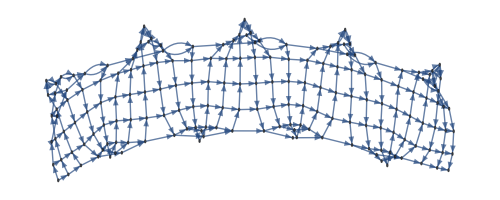
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","AB"->"AC","AC"->"CA","C"->"B"},"BBBAAAAA",200,SSSMax->40,NetMax->177,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,NetMax->179,VertexLabels->Placed["Name",Tooltip]];
```

```mathematica
SSSDisplay[%31,SSSMax->40,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,NetMax->177,VertexLabels->{x_:>Placed[x,Tooltip],1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}]
```

#### It’s not necessary to do the diagonal retrace to restart, since a new rule can simply restart the next right diagonal.

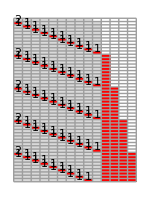
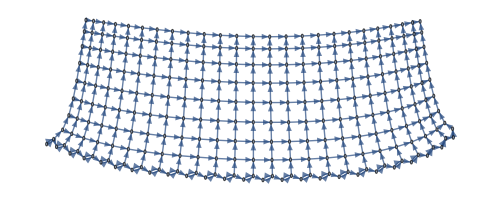
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","A"->"BA"},"AAAAAAAAA",250,SSSMax->50,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

#### 2-d: Incrementing the number of As at the beginning of each diagonal stroke turns the constant width band into a 2-d case.

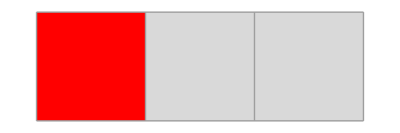
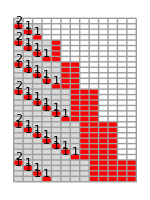
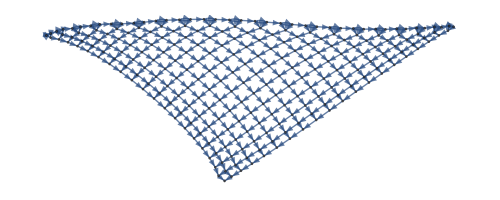
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","A"->"BAA"},"A",250,SSSMax->30,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

#### Exponential: Adding an extra A at the beginning of each diagonal stroke makes each pass one step longer, and turns the network into an exponential case.


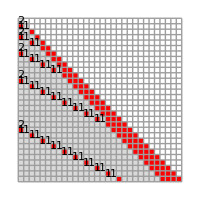
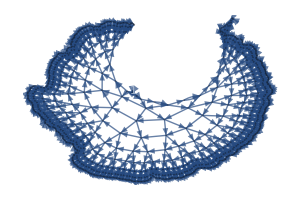
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AAB","A"->"BA"},"A",850,SSSMax->30,SSSSize->{200,200},NetSize->{300,200},RulePlacement->Left,
VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

#### 3-d: The constant increase can be changed to a linearly increasing effect by incrementing the number of As whenever the diagonal stroke passes a vertical bar (C), and adding in a new C at the beginning of each diagonal stroke. The entire network is now 3-dimensional.

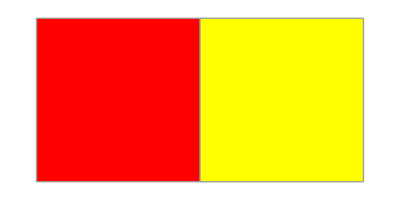
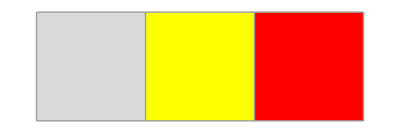
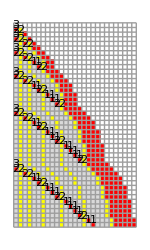
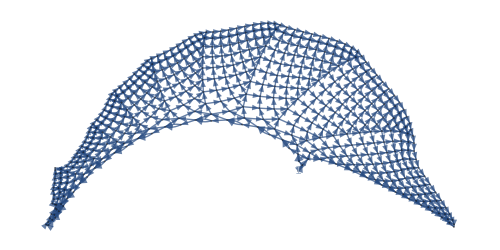
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss3d=SSS[{"BA"->"AB","BC"->"ACB","A"->"BC"},"A",500,SSSMax->44,SSSSize->{150,250},NetSize->{500,250},RulePlacement->Left,VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

```mathematica
SSSAnimate[sss3d]
```

#### 4-d: A quadratic increase is achieved by creating a C at the beginning of each diagonal stroke, a D whenever the diagonal stroke passes a C, and an A whenever it passes a D. The entire network is now 4-dimensional.

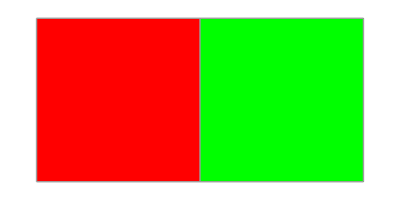
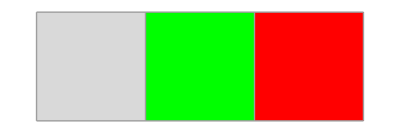
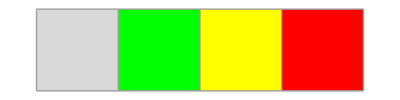
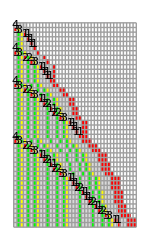
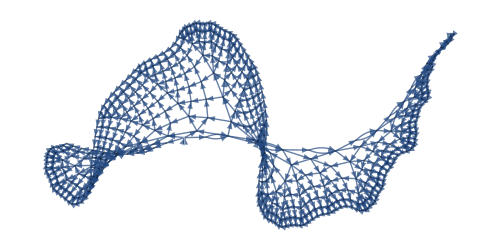
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss4d=SSS[{"BA"->"AB","BD"->"ADB","BC"->"ADCB","A"->"BC"},"AAAA",500,SSSMax->44,SSSSize->{150,250},NetSize->{500,250},RulePlacement->Left,VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

#### 5-d: Creating a C at the beginning of each diagonal stroke, a D whenever the diagonal stroke passes a C, an E whenever the diagonal stroke passes a D, and an A whenever it passes an E. The entire network is now 5-dimensional.

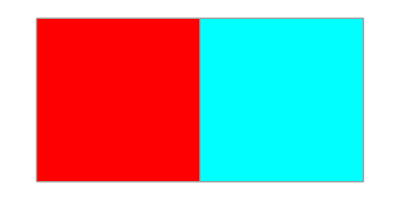
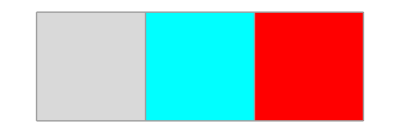
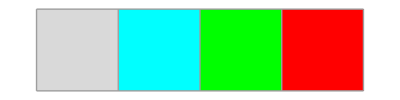
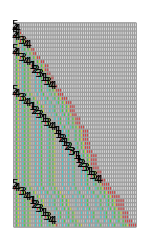
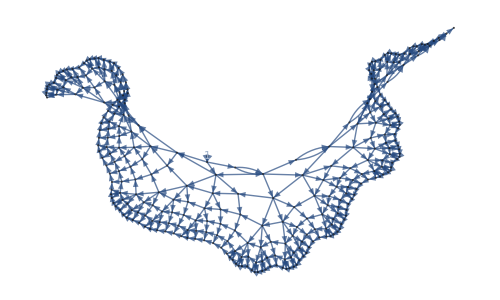
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss5d=SSS[{"BA"->"AB","BE"->"AEB","BD"->"AEDB","BC"->"ADCB","A"->"BC"},"A",323,SSSMax->50,SSSSize->{150,250},NetSize->{500,300},RulePlacement->Left,VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

#### 6-d

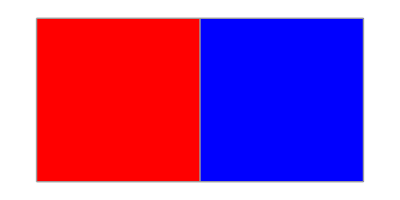
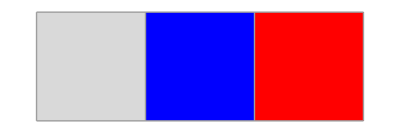
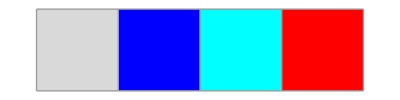
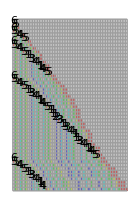
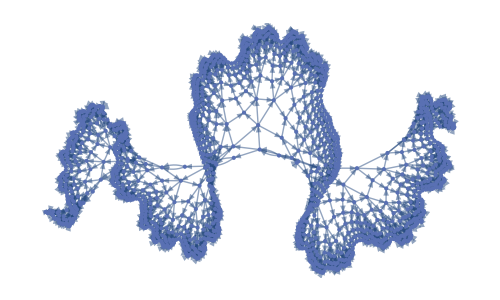
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","BF"->"AFB","BE"->"AFEB","BD"->"AEDB","BC"->"ADCB","A"->"BC"},"A",1500,SSSMax->50,SSSSize->{140,210},NetSize->{500,300},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

#### Other n-d cases

Try for n-dimensional, without the inert red section at the end:  needs one extra rule:

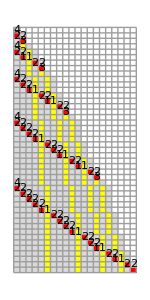
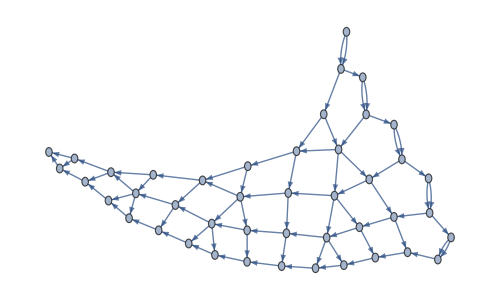
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BC"->"ACB","BA"->"AB","B"->"CA","A"->"BA"},"A",44,SSSSize->{150,300},NetSize->{500,300},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

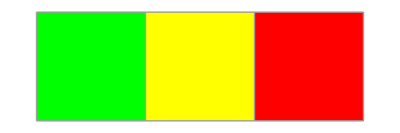
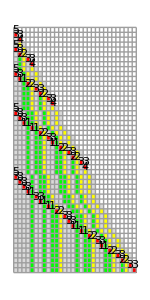
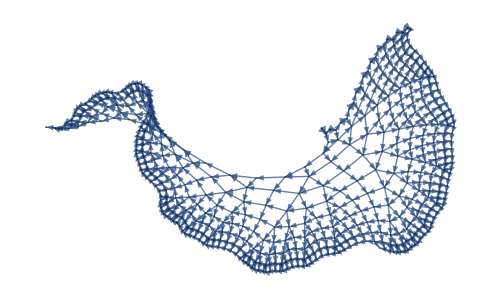
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BD"->"ADB","BC"->"DCB","BA"->"AB","B"->"CA","A"->"BA"},"A",500,SSSMax->50,SSSSize->{150,300},NetSize->{500,300},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

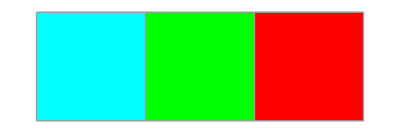
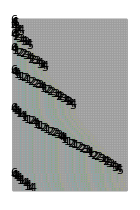
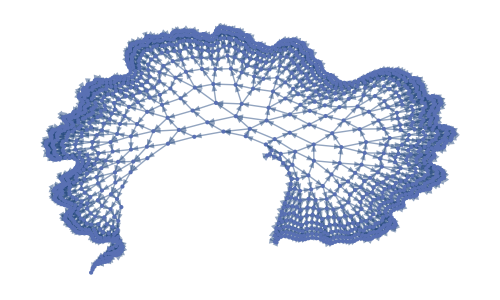
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BE"->"AEB","BD"->"EDB","BC"->"DCB","BA"->"AB","B"->"CA","A"->"BA"},"A",1500,SSSMax->100,SSSSize->{140,210},NetSize->{500,300},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

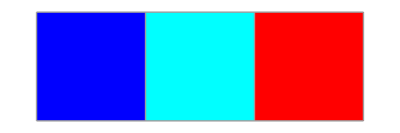
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BF"->"AFB","BE"->"FEB","BD"->"EDB","BC"->"DCB","BA"->"AB","B"->"CA","A"->"BA"},"A",5100,SSSMax->100,NetMax->700,SSSSize->{140,210},NetSize->{500,300},Mesh->False,RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```